## Measures of “Smoothness” of the graph

### Fourier Transform Measure

#### Depth

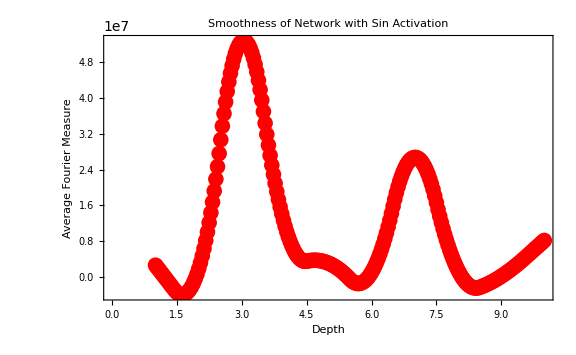

```mathematica
createAndInitializeNet[depth_,activation_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,1],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
evaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
depthLevels=Range[1,10];
averageSinFourierMeasures=Table[With[{netInit=createAndInitializeNet[depth,Sin]},Mean[Table[Module[{outputs=evaluateNet[netInit,Range[-3,3,0.01]],fTransform},fTransform=Abs[Fourier[outputs]];
Total[(Range[0,Length[outputs]-1]^2)*fTransform^2]],15 ]]],{depth,depthLevels}];
ListLinePlot[Transpose[{depthLevels,averageSinFourierMeasures}],Frame->True,FrameLabel->{"Depth","Average Fourier Measure"},PlotLabel->"Smoothness of Network with Sin Activation",PlotStyle->Thin,InterpolationOrder->2,Mesh->All,MeshStyle->Red,ImageSize->Large]
```

#### Sin and Sigmoid Together

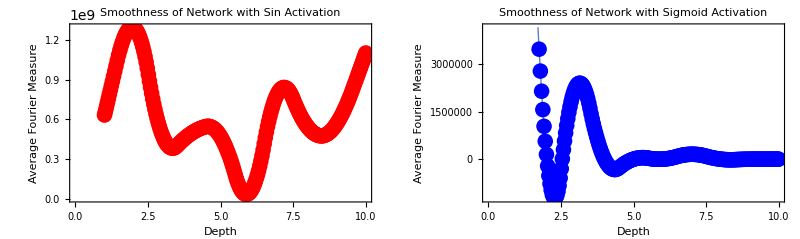

```mathematica
createAndInitializeNet[depth_,activation_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,2],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
evaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
depthLevels=Range[1,10];
measureFourier[activation_]:=Table[With[{netInit=createAndInitializeNet[depth,activation]},Mean[Table[Module[{outputs=evaluateNet[netInit,Range[-3,3,0.01]],fTransform},fTransform=Abs[Fourier[outputs]];
Total[(Range[0,Length[outputs]-1]^2)*fTransform^2]],15]]],{depth,depthLevels}];
averageSinFourierMeasures=measureFourier[Sin];
averageSigmoidFourierMeasures=measureFourier[LogisticSigmoid];
sinFourierPlot=ListLinePlot[Transpose[{depthLevels,averageSinFourierMeasures}],Frame->True,FrameLabel->{"Depth","Average Fourier Measure"},PlotLabel->"Smoothness of Network with Sin Activation",PlotStyle->Thick,InterpolationOrder->2,Mesh->All,MeshStyle->Red,ImageSize->Large];
sigmoidFourierPlot=ListLinePlot[Transpose[{depthLevels,averageSigmoidFourierMeasures}],Frame->True,FrameLabel->{"Depth","Average Fourier Measure"},PlotLabel->"Smoothness of Network with Sigmoid Activation",PlotStyle->Thick,InterpolationOrder->2,Mesh->All,MeshStyle->Blue,ImageSize->Large];
GraphicsGrid[{{sinFourierPlot,sigmoidFourierPlot}}]
```

#### Standard Deviation

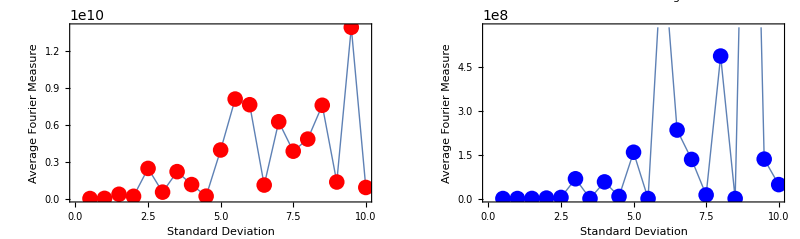

```mathematica
createAndInitializeNet[stdDev_,activation_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},3],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,stdDev],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
evaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
stdDevs=Range[0.5, 10, 0.5];
measureFourier[activation_]:=Table[With[{netInit=createAndInitializeNet[stdDev,activation]},Mean[Table[Module[{outputs=evaluateNet[netInit,Range[-3,3,0.01]],fTransform},fTransform=Abs[Fourier[outputs]];
Total[(Range[0,Length[outputs]-1]^2)*fTransform^2]],15]]],{stdDev,stdDevs}];
averageSinFourierMeasures=measureFourier[Sin];
averageSigmoidFourierMeasures=measureFourier[LogisticSigmoid];
sinFourierPlot=ListLinePlot[Transpose[{stdDevs,averageSinFourierMeasures}],Frame->True,FrameLabel->{"Standard Deviation","Average Fourier Measure"},PlotLabel->"Smoothness of Network with Sin Activation",PlotStyle->Thick,Mesh->All,MeshStyle->Red,ImageSize->Large];
sigmoidFourierPlot=ListLinePlot[Transpose[{stdDevs,averageSigmoidFourierMeasures}],Frame->True,FrameLabel->{"Standard Deviation","Average Fourier Measure"},PlotLabel->"Smoothness of Network with Sigmoid Activation",PlotStyle->Thick,Mesh->All,MeshStyle->Blue,ImageSize->Large];
GraphicsGrid[{{sinFourierPlot,sigmoidFourierPlot}}]
```

### Total Variance

#### Depth

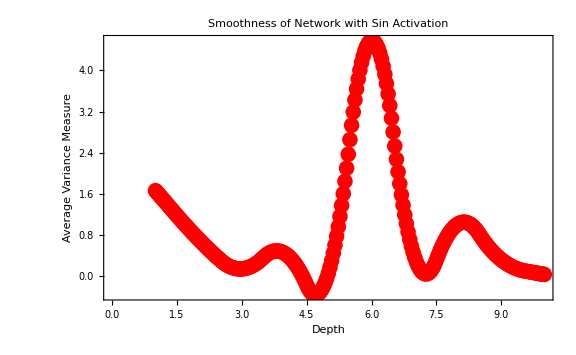

```mathematica
createAndInitializeNet[depth_,activation_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,1],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
evaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
depthLevels=Range[1,10];
averageSinVarianceMeasures=Table[With[{netInit=createAndInitializeNet[depth,Sin]},Mean[Table[Module[{outputs=evaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15 ]]],{depth,depthLevels}];
ListLinePlot[Transpose[{depthLevels,averageSinVarianceMeasures}],Frame->True,FrameLabel->{"Depth","Average Variance Measure"},PlotLabel->"Smoothness of Network with Sin Activation",PlotStyle->Thick,InterpolationOrder->2,Mesh->All,MeshStyle->Red,ImageSize->Large]
```

#### Sin and Sigmoid together

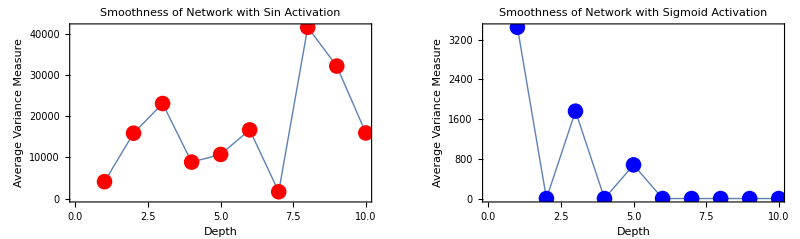

```mathematica
createAndInitializeNet[depth_,activation_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,100],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
evaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
depthLevels=Range[1,10];
measureVariance[activation_]:=Table[With[{netInit=createAndInitializeNet[depth,activation]},Mean[Table[Module[{outputs=evaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]],{depth,depthLevels}];
averageSinVarianceMeasures=measureVariance[Sin];
averageSigmoidVarianceMeasures=measureVariance[LogisticSigmoid];
sinPlot=ListLinePlot[Transpose[{depthLevels,averageSinVarianceMeasures}],Frame->True,FrameLabel->{"Depth","Average Variance Measure"},PlotLabel->"Smoothness of Network with Sin Activation",PlotStyle->Thick,Mesh->All,MeshStyle->Red,ImageSize->Large];
sigmoidPlot=ListLinePlot[Transpose[{depthLevels,averageSigmoidVarianceMeasures}],Frame->True,FrameLabel->{"Depth","Average Variance Measure"},PlotLabel->"Smoothness of Network with Sigmoid Activation",PlotStyle->Thick,Mesh->All,MeshStyle->Blue,ImageSize->Large];
GraphicsGrid[{{sinPlot,sigmoidPlot}}]
```

#### Standard Deviation

{0.0300633,0.107182,0.876638,2.15511,1.63816,9.80435,6.37565,10.1171,21.2728,28.5225,34.1653,65.2478,31.3837,56.2227,62.1023,79.9168,336.824,24.9935,83.3111,209.991}

{9.65558×10^-6,0.00142504,0.00519117,1.35325,0.00443957,0.00908362,0.0432719,8.63662×10^-6,1.45342×10^-11,39.6793,9.06329,2.82195,5.02861,1.06521,0.655161,1.67467,4.90398×10^-6,17.9393,1.52753,28.6253}

{{0.5,0.0300633},{1.,0.107182},{1.5,0.876638},{2.,2.15511},{2.5,1.63816},{3.,9.80435},{3.5,6.37565},{4.,10.1171},{4.5,21.2728},{5.,28.5225},{5.5,34.1653},{6.,65.2478},{6.5,31.3837},{7.,56.2227},{7.5,62.1023},{8.,79.9168},{8.5,336.824},{9.,24.9935},{9.5,83.3111},{10.,209.991}}

{{0.5,9.65558×10^-6},{1.,0.00142504},{1.5,0.00519117},{2.,1.35325},{2.5,0.00443957},{3.,0.00908362},{3.5,0.0432719},{4.,8.63662×10^-6},{4.5,1.45342×10^-11},{5.,39.6793},{5.5,9.06329},{6.,2.82195},{6.5,5.02861},{7.,1.06521},{7.5,0.655161},{8.,1.67467},{8.5,4.90398×10^-6},{9.,17.9393},{9.5,1.52753},{10.,28.6253}}

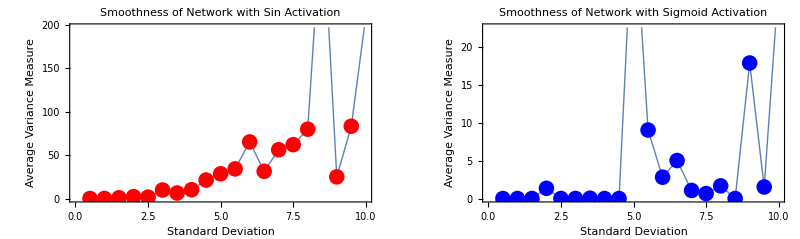

```mathematica
createAndInitializeNet[stdDev_,activation_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},3],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,stdDev],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
evaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
stdDevs=Range[0.5, 10, 0.5];
measureVariance[activation_]:=Table[With[{netInit=createAndInitializeNet[stdDev,activation]},Mean[Table[Module[{outputs=evaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]],{stdDev,stdDevs}];
averageSinVarianceMeasures=measureVariance[Sin];
averageSigmoidVarianceMeasures=measureVariance[LogisticSigmoid];
sinVariancePlot=ListLinePlot[Transpose[{stdDevs,averageSinVarianceMeasures}],Frame->True,FrameLabel->{"Standard Deviation","Average Variance Measure"},PlotLabel->"Smoothness of Network with Sin Activation",PlotStyle->Thick,Mesh->All,MeshStyle->Red,ImageSize->Large];
sigmoidVariancePlot=ListLinePlot[Transpose[{stdDevs,averageSigmoidVarianceMeasures}],Frame->True,FrameLabel->{"Standard Deviation","Average Variance Measure"},PlotLabel->"Smoothness of Network with Sigmoid Activation",PlotStyle->Thick,Mesh->All,MeshStyle->Blue,ImageSize->Large];
GraphicsGrid[{{sinVariancePlot,sigmoidVariancePlot}}]
```

## Explanation for Above Experiments

The above manipulations of depth and standard deviation were intended to provide a picture of the effect on the “smoothness” of the output graphs generated by 15 runs of a randomly initialized neural network at the depth/std dev combination. Two different activation functions, Sin and Sigmoid, were used because of they completely different output graphs they displayed. Interestingly, for the most part, both the Fourier Measure and the Total Variance graphs for each activation function strongly resembled each other in shape and characteristics, leading to the implication that standard deviation and network depth have similar effects on the output distributions for all types of activation functions, linear and non-linear. This could be because...

## Output Graphs for Logistic Sigmoid (Clamping?)

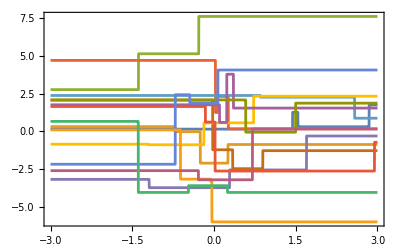
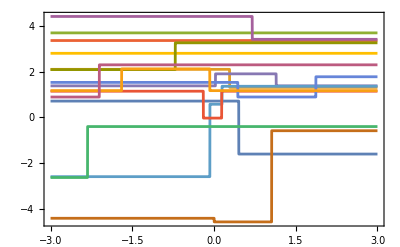
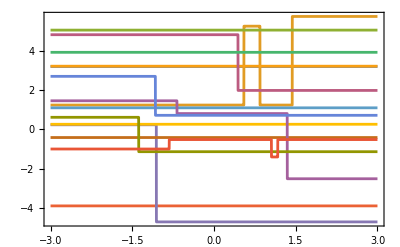
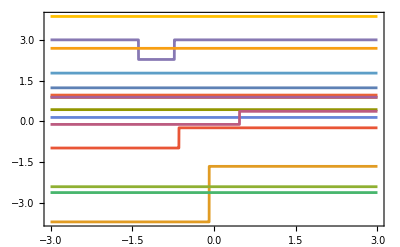
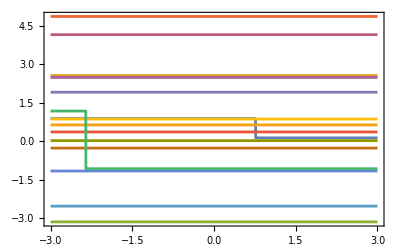
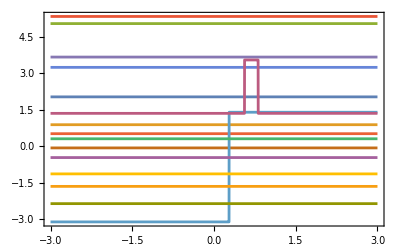
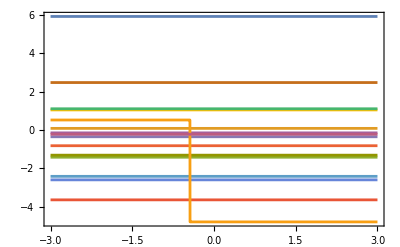
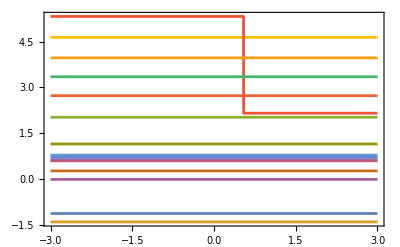
Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
With[{netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[10]},
SeedRandom[1234];
Grid[
Append[Prepend[netPlots,""]]@Table[
Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},
Plot[Evaluate@Flatten@Table[
Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[0, 2],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0, 1]]},RandomSeeding->Automatic],f},
f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]
],
15
],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None
]
],{depth,Range[10]}
],{act,{Function[x,If[x>0,1,0]],Tanh,LogisticSigmoid}}]
]
]
```

### Explanation of Clamping

As you can see here, despite the fact that Sigmoid is a distinctly non-linear function, past a certain depth (in this case 5), the output graphs become almost completely straight. At first glance, this seems quite surprising, as the tanh function (very similar in shape to the Sigmoid) never reaches such a state, and the piecewise linear Threshold function takes longer to reach it. It begs the question: What is so special about the Sigmoid function?

This question has a few parts. Firstly, and most importantly, the Sigmoid function can only output values between 0 and 1. This is the key difference between Sigmoid and tanh, and it’s the reason why one produces flatlining output graphs as depth increases, while the other produces increasingly complicated ones.............

## Same thing but for Standard Deviation, see if that also contributes to Clamping

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[std dev = 0.1][std dev = 0.1].

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[std dev = 0.5][std dev = 0.5].

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[std dev = 1][std dev = 1].

General::stop: Further output of Prepend::normal will be suppressed during this calculation.

Threshold | Prepend[std dev = 0.1][std dev = 0.1] | Prepend[std dev = 0.5][std dev = 0.5] | Prepend[std dev = 1][std dev = 1] | Prepend[std dev = 2][std dev = 2] | Prepend[std dev = 5][std dev = 5]
Sin | Prepend[std dev = 0.1][std dev = 0.1] | Prepend[std dev = 0.5][std dev = 0.5] | Prepend[std dev = 1][std dev = 1] | Prepend[std dev = 2][std dev = 2] | Prepend[std dev = 5][std dev = 5]
LogisticSigmoid | Prepend[std dev = 0.1][std dev = 0.1] | Prepend[std dev = 0.5][std dev = 0.5] | Prepend[std dev = 1][std dev = 1] | Prepend[std dev = 2][std dev = 2] | Prepend[std dev = 5][std dev = 5]
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-